# Introgressive hybridization: balancing genetic and demographic swamping

## Freek J.H. de Haas & Sarah P. Otto

University of British Columbia

Contact: freekdh@gmail.com

## Preliminaries

```mathematica
(*for uniformity among figures*)
LabelSize=25;
FigureSize=650;
TickSize=16;
LetterSize=20;
Pad={{70,25},{70,10}};
letpos={.05,.93};
ylabpos={-0.1,0.5};

SetDirectory[NotebookDirectory[]];

(*directory to save figures in*)
imagedir="../Figures/";

(*for plotting means with error bars*)
Needs["ErrorBarPlots`"]
```

## Numerical solution haploids

Assuming exponential growth of the invader and resident assumes that the populations remain small. When populations are larger, density dependence should be taken into account.

```mathematica
param={rRes->Log[0.1],rInv->Log[1.01],kRes->10,kInv->1,Θ->1};
```

```mathematica
nRes[t_]:=kRes*Exp[(t)*rRes];
nInv[t_]:=kInv*Exp[(t)*rInv];
```

```mathematica
Clear[simulatefrac]
simulatefrac[t_,rRes_,rInv_,kRes_,kInv_,Θ_]:=simulatefrac[t,rRes,rInv,kRes,kInv,Θ]=
Block[{
fracRes=simulatefrac[t-1,rRes,rInv,kRes,kInv,Θ][[1]],
fracInv=simulatefrac[t-1,rRes,rInv,kRes,kInv,Θ][[2]]},

nRes[t-1]=kRes*Exp[(t-1)*rRes];
nInv[t-1]=kInv*Exp[(t-1)*rInv];
newfracRes=(1/2*fracRes+1/2*fracInv)*nInv[t-1]/(nInv[t-1]+nRes[t-1]Θ)+(fracRes)*(nRes[t-1]Θ)/(nInv[t-1]+nRes[t-1]Θ);(*This is the equation describing how the genomic background changes for an individual carrying A, depending on who it mates with.*)
newfracInv=(1/2*fracRes+1/2*fracInv)*nRes[t-1]/(nInv[t-1]Θ+nRes[t-1])+(fracInv)*(nInv[t-1]Θ)/(nInv[t-1]Θ+nRes[t-1]);
(*This is the equation describing how the genomic background changes for an individual carrying a, depending on who it mates with.*)
{newfracRes,newfracInv} 
]
simulatefrac[0,rRes/.param,rInv/.param,kRes/.param,kInv/.param,Θ/.param]={1,0};
```

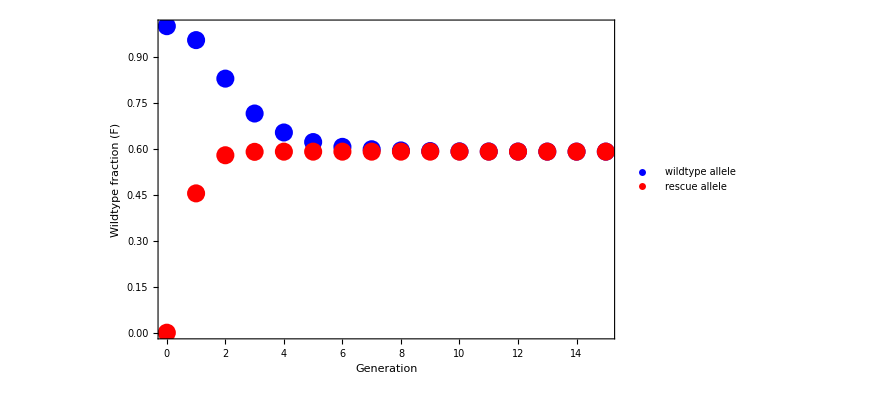

```mathematica
plot=Legended[
Show[
ListPlot[Table[{t,simulatefrac[t,rRes/.param,rInv/.param,kRes/.param,kInv/.param,Θ/.param][[1]]},{t,0,15}],PlotStyle->{PointSize[0.02],Blue},PlotRange->{{0,15},{0,1}}],
ListPlot[Table[{t,simulatefrac[t,rRes/.param,rInv/.param,kRes/.param,kInv/.param,Θ/.param][[2]]},{t,0,15}],PlotStyle->{PointSize[0.02],Red},PlotRange->{{0,15},{0,1}}],
Frame->True,
FrameLabel->{Style["Generation",LabelSize],Style["Wildtype fraction (F)",LabelSize]},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangeClipping->False
],
Placed[
PointLegend[{
{Blue,AbsolutePointSize[10]},{Red,AbsolutePointSize[10]},NULL
},
{
Style["wildtype allele",LabelSize],
Style["rescue allele",LabelSize]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{.82,0.12}
] 
]
```

```mathematica
Export[imagedir<>"NumericalSolution.eps",plot];
```

## Analytical solution

### Continuous time solution

```mathematica
param={rRes->Log[0.1*1.01],rInv->Log[1.0*1.01],kRes->10,kInv->1};
```

Set up differential equations by substracting ΔfracRes = fracRes[t+1] - fracRes[t] & ΔfracInv = fracInv[t+1] - fracInv[t]

```mathematica
DfracRes= (1/2*fracRes[t]+1/2*fracInv[t])*(kInv*Exp[t*rInv])/(kInv*Exp[t*rInv]+kRes*Exp[t*rRes])+(fracRes[t])*(kRes*Exp[t*rRes])/(kInv*Exp[t*rInv]+kRes*Exp[t*rRes])-fracRes[t];
DfracInv=(1/2*fracRes[t]+1/2*fracInv[t])*(kRes*Exp[t*rRes])/(kInv*Exp[t*rInv]+kRes*Exp[t*rRes])+(fracInv[t])*(kInv*Exp[t*rInv])/(kInv*Exp[t*rInv]+kRes*Exp[t*rRes])-fracInv[t];
```

To solve these differential equations, use avg[t] and dif[t] as substitutions

```mathematica
subme=Solve[{sum[t]==fracInv[t]+fracRes[t],dif[t]==fracRes[t]-fracInv[t]},{fracInv[t],fracRes[t]}][[1]];
```

```mathematica
Ddif=DfracRes-DfracInv/.subme//Simplify;
Dsum =DfracRes+DfracInv/.subme//Simplify;
```

Plot numerical solution of dif[t] and sum[t]

```mathematica
solvemeN2[kRes_,rRes_,kInv_,rInv_]:=NDSolve[{D[dif[t],t]==-dif[t]/2,D[sum[t],t]==((-ⅇ^(rInv t) kInv+ⅇ^(rRes t) kRes) dif[t])/(2 (ⅇ^(rInv t) kInv+ⅇ^(rRes t) kRes)),dif[0]==1,sum[0]==1},{dif[t],sum[t]},{t,0,50}];
```

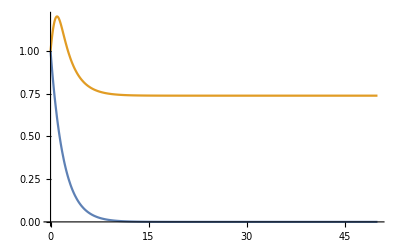

```mathematica
Plot[{
Evaluate[dif[t]/.solvemeN2[kRes/.param,rRes/.param,kInv/.param,rInv/.param]],
Evaluate[sum[t]/.solvemeN2[kRes/.param,rRes/.param,kInv/.param,rInv/.param]]},{t,0,50}]
```

Solution for dif[t] is easy to find:

```mathematica
DSolve[{D[dif[t],t]==-dif[t]/2,dif[0]==1},{dif[t]},t][[1]]
```

{dif[t]→ⅇ^(-t/2)}

Solution for sum[t] is a bit harder:

```mathematica
((-ⅇ^(rInv t) kInv+ⅇ^(rRes t) kRes) dif[t])/(2 (ⅇ^(rInv t) kInv+ⅇ^(rRes t) kRes))/.dif[t]->ⅇ^(-t/2)/.kInv->kRat*kRes/.rRes->rRat+rInv/.rRat->Log[RRat]//Simplify
```

(ⅇ^(-t/2) (-kRat+RRat^t))/(2 (kRat+RRat^t))

```mathematica
Simplify[∫(ⅇ^(-t/2) ((ⅇ^rRat)^t-kRat))/(2 ((ⅇ^rRat)^t+kRat))ⅆt,{kRat>0}]
```

ⅇ^(-t/2) (-1+2 Hypergeometric2F1[1,-1/(2 Log[ⅇ^rRat]),1-1/(2 Log[ⅇ^rRat]),-((ⅇ^rRat)^t)/kRat])

Find the constant of integration (coi)

```mathematica
Solve[1==(ⅇ^(-t/2) (-1+2 Hypergeometric2F1[1,-1/(2 Log[ⅇ^rRat]),1-1/(2 Log[ⅇ^rRat]),-((ⅇ^rRat)^t)/kRat])/.t->0)+coi,coi][[1]]
```

{coi→-2 (-1+Hypergeometric2F1[1,-1/(2 Log[ⅇ^rRat]),1-1/(2 Log[ⅇ^rRat]),-1/kRat])}

Adding the coi we get the full solution:

```mathematica
FullSolution=ⅇ^(-t/2) (-1+2 Hypergeometric2F1[1,-1/(2 Log[ⅇ^rRat]),1-1/(2 Log[ⅇ^rRat]),-((ⅇ^rRat)^t)/kRat])-2 (-1+Hypergeometric2F1[1,-1/(2 Log[ⅇ^rRat]),1-1/(2 Log[ⅇ^rRat]),-1/kRat])//FullSimplify
```

2-2 Hypergeometric2F1[1,-1/(2 Log[ⅇ^rRat]),1-1/(2 Log[ⅇ^rRat]),-1/kRat]+ⅇ^(-t/2) (-1+2 Hypergeometric2F1[1,-1/(2 Log[ⅇ^rRat]),1-1/(2 Log[ⅇ^rRat]),-((ⅇ^rRat)^t)/kRat])

The third component of this formula goes to 0 in the limit of t->Infinity, so we are left with:

```mathematica
Simplify[2-2 Hypergeometric2F1[1,-1/(2 Log[ⅇ^rRat]),1-1/(2 Log[ⅇ^rRat]),-1/kRat],rRat>0]
```

2-2 Hypergeometric2F1[1,-1/(2 rRat),1-1/(2 rRat),-1/kRat]

This is the sum[Inf] solution; as dif[Inf] goes to 0, 1/2 F_I[Inf]=1/2 F_R[Inf]=Sum[Inf]

```mathematica
1/2(2-2 Hypergeometric2F1[1,-1/(2 rRat),1-1/(2 rRat),-1/kRat])//Simplify
```

1-Hypergeometric2F1[1,-1/(2 rRat),1-1/(2 rRat),-1/kRat]

#### Approximating hypergeometric 1-Hypergeometric2F1[1,-1/(2 rRat),1-1/(2 rRat),-1/kRat]

```mathematica
Normal[Series[1-1Hypergeometric2F1[1,-1/(2 rRat),1-1/(2 rRat),-1/kRat]/.rRat->Log[RRat],{kRat,0,1}]]//FullSimplify
```

1-(ⅇ^((ⅈ π Floor[(π+Arg[kRat])/(2 π)])/Log[RRat]) kRat^(-1/(2 Log[RRat])) π Csc[π/(2 Log[RRat])])/(2 Log[RRat])-kRat/(1+2 Log[RRat])

```mathematica
Plot[1-(ⅇ^((ⅈ π Floor[(π+Arg[kRat])/(2 π)])/Log[RRat]) kRat^(-1/(2 Log[RRat])) π Csc[π/(2 Log[RRat])])/(2 Log[RRat])-kRat/(1+2 Log[RRat]),{RRat,0,1}];
```

```mathematica
ShowFunc[kRat_]:=Show[
ListPlot[Table[{RRat,1- Hypergeometric2F1[1,-1/(2 Log[RRat]),1-1/(2 Log[RRat]),-1/kRat]},{RRat,0.01,0.99,0.001}],PlotRange->{{0,1},{0,1}}],
Plot[1-kRat^(-1/(2Log[RRat])),{RRat,0,1},PlotStyle->Red],
Plot[1-(kRat)^RRat,{RRat,0,1},PlotStyle->Blue],
Plot[(1-kRat^(-1/(2 Log[RRat])))*(1-RRat)+(1-(kRat)^(RRat))*RRat,{RRat,0,1},PlotStyle->Purple]]
```

```mathematica
(1-kRat^(-1/(2 Log[RRat])))*(1-RRat)+(1-(kRat)^(RRat))*RRat//Simplify
```

1+kRat^(-1/(2 Log[RRat])) (-1+RRat)-kRat^RRat RRat

```mathematica
Plot3D[(1-kRat^(-1/(2 Log[RRat])))*(1-RRat)+(1-(kRat)^(RRat))*RRat,{kRat,0,1},{RRat,0,1}]
```

-Graphics3D-

```mathematica
Plot3D[(1-kRat^(-1/(2 Log[RRat]))),{kRat,0,1},{RRat,0,1}]
```

-Graphics3D-

```mathematica
Plot3D[1- Hypergeometric2F1[1,-1/(2 Log[RRat]),1-1/(2 Log[RRat]),-1/kRat],{kRat,0,0.99},{RRat,0,0.99}]
```

-Graphics3D-

```mathematica
Manipulate[Show[
Plot[(1-kRat^RRat)/.kRat->0.1,{RRat,0,1},PlotRange->{Automatic,{0,1}},PlotStyle->Red],
Plot[1-2^(-(100+1))-∑_(j=0)^(100-1) (2^(-1-j) kRat)/(ⅇ^(eRRat j)+kRat)/.eRRat->Log[RRat]/.kRat->0.1,{RRat,0.01,0.99}]],{kRat,0.01,0.99}]
```

#### Itteration vs Continuous solution

```mathematica
Clear[solvemeN]
solvemeN[kRes_,rRes_,kInv_,rInv_]:=NDSolve[{
D[fracRes[t],t]== (1/2*fracRes[t]+1/2*fracInv[t])*(kInv*Exp[t*rInv])/(kInv*Exp[t*rInv]+kRes*Exp[t*rRes])+(fracRes[t])*(kRes*Exp[t*rRes])/(kInv*Exp[t*rInv]+kRes*Exp[t*rRes])-fracRes[t],
D[fracInv[t],t]==(1/2*fracRes[t]+1/2*fracInv[t])*(kRes*Exp[t*rRes])/(kInv*Exp[t*rInv]+kRes*Exp[t*rRes])+(fracInv[t])*(kInv*Exp[t*rInv])/(kInv*Exp[t*rInv]+kRes*Exp[t*rRes])-fracInv[t],
fracRes[0]==1,
fracInv[0]==0},{fracRes[t],fracInv[t]},{t,0,50}]
```

```mathematica
param={rRes->Log[0.1*1.01],rInv->Log[1.0*1.01],kRes->10,kInv->1};
```

```mathematica
simulatefrac[0,rRes/.param,rInv/.param,kRes/.param,kInv/.param]={1,0};
Show[
Plot[Evaluate[fracRes[t]/.solvemeN[kRes/.param,rRes/.param,kInv/.param,rInv/.param][[1]]],{t,0,50},PlotRange->{{0,50},{0,1}},PlotStyle->{Red}],
Plot[Evaluate[fracInv[t]/.solvemeN[kRes/.param,rRes/.param,kInv/.param,rInv/.param][[1]]],{t,0,50},PlotRange->{{0,50},{0,1}},PlotStyle->{Green}],
ListPlot[Table[{t,simulatefrac[t,rRes/.param,rInv/.param,kRes/.param,kInv/.param][[1]]},{t,0,50}],PlotStyle->{Dotted,Red},PlotRange->{{0,50},{0,10}}],
ListPlot[Table[{t,simulatefrac[t,rRes/.param,rInv/.param,kRes/.param,kInv/.param][[2]]},{t,0,50}],PlotStyle->{Dotted,Green},PlotRange->{{0,50},{0,10}}]
]
```

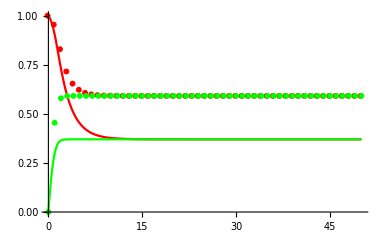

```mathematica
param={rRes->Log[0.9*1.01],rInv->Log[1.0*1.01],kRes->10,kInv->1};
```

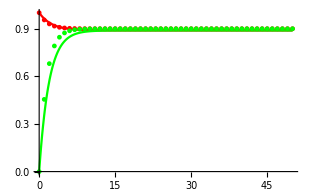

```mathematica
simulatefrac[0,rRes/.param,rInv/.param,kRes/.param,kInv/.param]={1,0};
Show[
Plot[Evaluate[fracRes[t]/.solvemeN[kRes/.param,rRes/.param,kInv/.param,rInv/.param][[1]]],{t,0,50},PlotRange->{{0,50},{0,1}},PlotStyle->{Red}],
Plot[Evaluate[fracInv[t]/.solvemeN[kRes/.param,rRes/.param,kInv/.param,rInv/.param][[1]]],{t,0,50},PlotRange->{{0,50},{0,1}},PlotStyle->{Green}],
ListPlot[Table[{t,simulatefrac[t,rRes/.param,rInv/.param,kRes/.param,kInv/.param][[1]]},{t,0,50}],PlotStyle->{Dotted,Red},PlotRange->{{0,50},{0,10}}],
ListPlot[Table[{t,simulatefrac[t,rRes/.param,rInv/.param,kRes/.param,kInv/.param][[2]]},{t,0,50}],PlotStyle->{Dotted,Green},PlotRange->{{0,50},{0,10}}]
]
```

Conclusions: when viability resident (VRES) is low, analytical deviates a lot from numerical prediction. When VRES is high (0.9), analytical is similar to numerical prediction.

### Discrete time solution

```mathematica
subme=Solve[{ave[t]==(fracInv[t]+fracRes[t])/2,dif[t]==fracRes[t]-fracInv[t]},{fracInv[t],fracRes[t]}][[1]];
```

```mathematica
fracResprime= (1/2*fracRes[t]+1/2*fracInv[t])*(kInv*Exp[t*rInv])/(kInv*Exp[t*rInv]+kRes*Exp[t*rRes])+(fracRes[t])*(kRes*Exp[t*rRes])/(kInv*Exp[t*rInv]+kRes*Exp[t*rRes]);
fracInvprime=(1/2*fracRes[t]+1/2*fracInv[t])*(kRes*Exp[t*rRes])/(kInv*Exp[t*rInv]+kRes*Exp[t*rRes])+(fracInv[t])*(kInv*Exp[t*rInv])/(kInv*Exp[t*rInv]+kRes*Exp[t*rRes]);
difprime=fracResprime-fracInvprime/.subme//Simplify
aveprime =(fracResprime+fracInvprime)/2/.subme//FullSimplify
```

dif[t]/2

ave[t]+1/4 (1-(2 ⅇ^(rInv t) kInv)/(ⅇ^(rInv t) kInv+ⅇ^(rRes t) kRes)) dif[t]

```mathematica
RSolve[{dif[t+1]==dif[t]/2,dif[0]==1},dif[t],t]
```

{{dif[t]→2^-t}}

```mathematica
FullSimplify[PowerExpand[aveprime/. dif[t]->2^-t/.kInv->kRes*kRat/.rRes->Log[RRes]/.rInv->Log[RInv]/.RRes->RInv*RRat],{RRat>0,kRat>0}]
```

(2^(-2-t) (-kRat+RRat^t+2^(2+t) (kRat+RRat^t) ave[t]))/(kRat+RRat^t)

This has a somewhat simpler form if we right RRat as an exponential function RRat = Exp[eRRat] :

```mathematica
FullSimplify[%/.RRat->Exp[eRRat],{eRRat>0,kRat>0}]
```

1/(2^(2+t)+(2^(3+t) kRat)/(ⅇ^(eRRat t)-kRat))+ave[t]

```mathematica
FullSimplify[PowerExpand[RSolve[{ave[t+1]==1/(2^(2+t)+(2^(3+t) kRat)/(ⅇ^(eRRat t)-kRat))+ave[t],ave[0]==1/2},ave[t],t]],{RRat>0,kRat>0}]/.K[1]->j
```

$Aborted

```mathematica
Solve[{ave[t]==1/2+∑_(j=0)^(-1+t) (2^(-2-j)(ⅇ^(eRRat j)-kRat))/(ⅇ^(eRRat j)+kRat),dif[t]==2^-t,ave[t]==(FI[t]+FR[t])/2,dif[t]==FI[t]-FR[t]},FI[t]]
```

$Aborted

The term in the sum can be simplified as follows:(2^(-2-j) (ⅇ^(eRRat j)-kRat))/(ⅇ^(eRRat j)+kRat) =2^(-2-j)-(2^(-1-j) kRat)/(ⅇ^(eRRat j)+kRat) This allows us to simplify the average as:1/2+∑_(j=0)^(t-1) 2^(-2-j)-∑_(j=0)^(t-1) (2^(-1-j) kRat)/(ⅇ^(eRRat j)+kRat)1-2^(-(t+1))-∑_(j=0)^(t-1) (2^(-1-j) kRat)/(ⅇ^(eRRat j)+kRat)
The term summed shows substantial change from generation to generation,but rapidly declines in value:

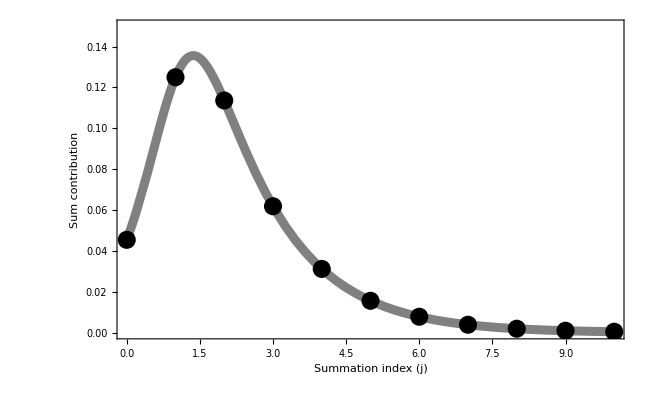

```mathematica
Show[
Plot[(2^(-1-j) kRat)/(ⅇ^(eRRat j)+kRat)/.eRRat->Log[RRat]/.kRat->0.1/.RRat->0.1,{j,0,10},PlotRange->{Automatic,{0,0.15}}, PlotStyle->{Thickness[0.01],Gray}],
ListPlot[Table[{j,(2^(-1-j) kRat)/(ⅇ^(eRRat j)+kRat)/.eRRat->Log[RRat]/.kRat->0.1/.RRat->0.1},{j,0,10}],PlotStyle->{PointSize[0.02],Black}],
Frame->True,
FrameLabel->{Style["Summation index (j)",LabelSize],Style["Sum contribution",LabelSize]},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangeClipping->False
]
```

```mathematica
Export[imagedir<>"SummationContribution.eps",%];
```

A numerical evaluation of the average fraction of the genome that is from the resident (evaluated at t = 100)

```mathematica
(2^(-1-j) kRat)/(ⅇ^(eRRat j)+kRat)/.eRRat->Log[RRat]
```

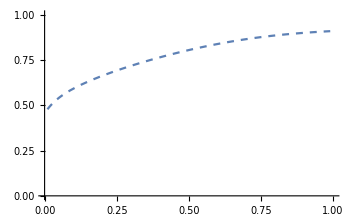

```mathematica
plot=Plot[1-2^(-(100+1))-∑_(j=0)^(100-1) (2^(-1-j) kRat)/(ⅇ^(eRRat j)+kRat)/.eRRat->Log[RRat]/.kRat->.1,{RRat,0.01,0.99},PlotStyle->Dashed,PlotRange->{{0,1},{0,1}}]
```

```mathematica
(2^(-1-j) kRat)/(ⅇ^(eRRat j)+kRat)/.eRRat->Log[RRat]/.j->10
```

kRat/(2048 (kRat+RRat^10))

```mathematica
Solve[kRat/(2048 (kRat))<0.01]
```

{{}}

Replacing the sum with an integral :

```mathematica
Integrate[(2^(-1-j) kRat)/(ⅇ^(eRRat j)+kRat),j];
soln=(1-2^(-(t+1))-((%/.j->(t-1))-(%/.j->0)))
```

1-2^(-1-t)-Hypergeometric2F1[1,-Log[2]/eRRat,1-Log[2]/eRRat,-1/kRat]/(2 Log[2])+(2^-t Hypergeometric2F1[1,-Log[2]/eRRat,1-Log[2]/eRRat,-ⅇ^(eRRat (-1+t))/kRat])/Log[2]

The result (black) is close to the sum evaluated directly (dashed), but not perfect :

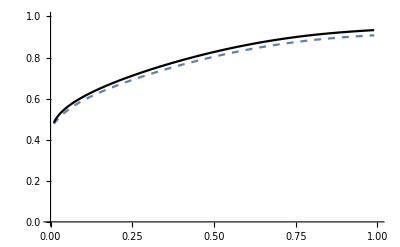

```mathematica
plotINT=Show[plot,Plot[soln/.eRRat->Log[RRat]/.kRat->0.1/.t->100,{RRat,0.01,0.99},PlotStyle->Black]]
```

A much improved solution is obtained by shifting the integration interval to be "centred" around the points that we' re trying to sum (e.g., from - 1/2 to + 1/2 to estimate the height at j = 0 ... and from (t - 1 - 1/2) to (t - 1 + 1/2) to estimate the height at t - 1) :

```mathematica
Integrate[(2^(-1-j) kRat)/(ⅇ^(eRRat j)+kRat),j];
newsoln=(1-2^(-(t+1))-((%/.j->(t-1)+1/2)-(%/.j->-1/2)))
```

1-2^(-1-t)-Hypergeometric2F1[1,-Log[2]/eRRat,1-Log[2]/eRRat,-ⅇ^(-eRRat/2)/kRat]/(√2 Log[2])+(2^(-1/2-t) Hypergeometric2F1[1,-Log[2]/eRRat,1-Log[2]/eRRat,-ⅇ^(eRRat (-1/2+t))/kRat])/Log[2]

The result (black) is close to the sum evaluated directly (dashed):

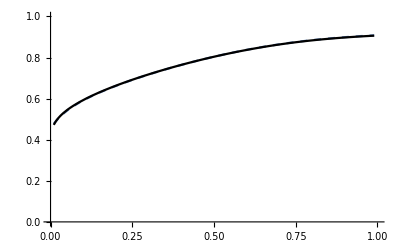

```mathematica
plotINT=Show[plot,Plot[newsoln/.eRRat->Log[RRat]/.kRat->0.1/.t->100,{RRat,0.01,0.99},PlotStyle->Black]]
```

An alternative takes out the j=0 term and integrates the rest:

```mathematica
Integrate[(2^(-1-j) kRat)/(ⅇ^(eRRat j)+kRat),j]
```

-(2^(-1-j) Hypergeometric2F1[1,-Log[2]/eRRat,1-Log[2]/eRRat,-ⅇ^(eRRat j)/kRat])/Log[2]

```mathematica
soln1=1-2^(-(t+1))-kRat/(2 (1+kRat))-((%/.j->t-1)-(%/.j->1))
```

1-2^(-1-t)-kRat/(2 (1+kRat))-Hypergeometric2F1[1,-Log[2]/eRRat,1-Log[2]/eRRat,-ⅇ^eRRat/kRat]/(4 Log[2])+(2^-t Hypergeometric2F1[1,-Log[2]/eRRat,1-Log[2]/eRRat,-ⅇ^(eRRat (-1+t))/kRat])/Log[2]

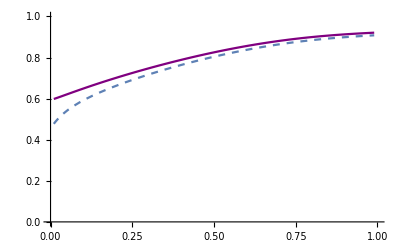

```mathematica
plot1=Show[plot,Plot[soln1/.eRRat->Log[RRat]/.kRat->0.1/.t->100,{RRat,0.01,0.99},PlotStyle->Purple]]
```

An alternative takes out the j = 0 and the j = 1 term and integrates the rest :

```mathematica
Integrate[(2^(-1-j) kRat)/(ⅇ^(eRRat j)+kRat),j];
```

```mathematica
soln2=1-2^(-(t+1))-kRat/(2 (1+kRat))-kRat/(8 (ⅇ^(2 eRRat)+kRat))-((%/.j->t-1)-(%/.j->2))
```

1-2^(-1-t)-kRat/(2 (1+kRat))-kRat/(8 (ⅇ^(2 eRRat)+kRat))-Hypergeometric2F1[1,-Log[2]/eRRat,1-Log[2]/eRRat,-ⅇ^(2 eRRat)/kRat]/(8 Log[2])+(2^-t Hypergeometric2F1[1,-Log[2]/eRRat,1-Log[2]/eRRat,-ⅇ^(eRRat (-1+t))/kRat])/Log[2]

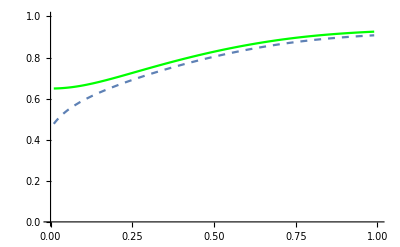

```mathematica
plot2=Show[plot,Plot[soln2/.eRRat->Log[RRat]/.kRat->0.1/.t->100,{RRat,0.01,0.99},PlotStyle->Green]]
```

But these solutions aren’t helping much.
Asymptote
Let’s next focus on the asymptote.When t is large,-2^(-1-t)can be ignored,as can(2^(-1/2-t) Hypergeometric2F1[1,-Log[2]/eRRat,1-Log[2]/eRRat,-ⅇ^(eRRat (-1/2+t))/kRat])/Log[2].The latter can be shown as follows.First,it is multiplied by2^(-1/2-t),which gets smaller as t gets larger.Second,the hypergeometric function can be written as a sum (see Abromowitz and Stegun 15.1.1):

```mathematica
Sum[(Pochhammer[1,n]Pochhammer[-Log[2]/eRRat,n])/Pochhammer[1-Log[2]/eRRat,n] z^n/(n!),{n,0,Infinity}]
```

Hypergeometric2F1[1,-Log[2]/eRRat,1-Log[2]/eRRat,z]

where z=-ⅇ^(eRRat (-1/2+t))/kRat=-RRat^(-1/2+t)/kRat.Assuming 0<RRat<1,thenRRat^(-1+t)will be small for very large t and z will approach zero.Consequently,the leading order term in the above sum is the n=0th term,which is just one:

```mathematica
(Pochhammer[1,n]Pochhammer[-Log[2]/eRRat,n])/Pochhammer[1-Log[2]/eRRat,n] z^n/(n!)/.n->0
```

1

This allows us to simplify the solution to1-Hypergeometric2F1[1,-Log[2]/eRRat,1-Log[2]/eRRat,-ⅇ^(-eRRat/2)/kRat]/(√2 Log[2]):

```mathematica
Infinity
```

^2 ∞

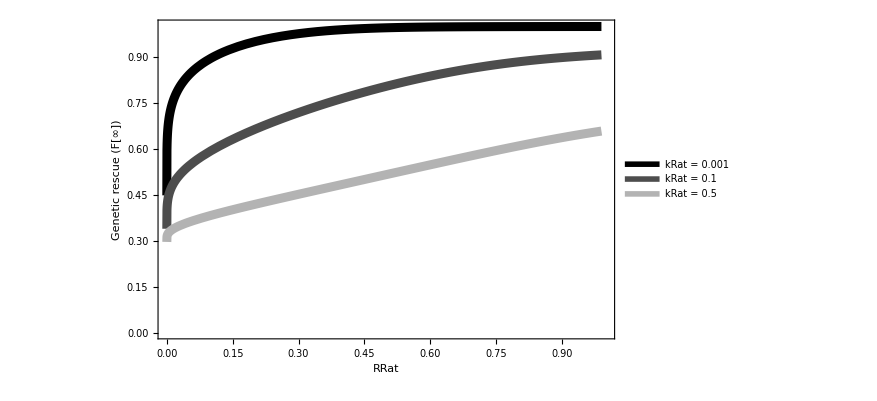

```mathematica
Legended[
Show[
Plot[1-Hypergeometric2F1[1,-Log[2]/eRRat,1-Log[2]/eRRat,-ⅇ^(-eRRat/2)/kRat]/(√2 Log[2])/.eRRat->Log[RRat]/.kRat->0.001,{RRat,0,0.99},PlotRange->{{0,1},{0,1}},PlotStyle->{Thickness[0.01],Black}],
Plot[1-Hypergeometric2F1[1,-Log[2]/eRRat,1-Log[2]/eRRat,-ⅇ^(-eRRat/2)/kRat]/(√2 Log[2])/.eRRat->Log[RRat]/.kRat->.1,{RRat,0,0.99},PlotRange->{{0,1},{0,1}},PlotStyle->{Thickness[0.01],GrayLevel[0.3]}],
Plot[1-Hypergeometric2F1[1,-Log[2]/eRRat,1-Log[2]/eRRat,-ⅇ^(-eRRat/2)/kRat]/(√2 Log[2])/.eRRat->Log[RRat]/.kRat->0.5,{RRat,0,0.99},PlotRange->{{0,1},{0,1}},PlotStyle->{Thickness[0.01],GrayLevel[0.7]}],
Frame->True,
FrameLabel->{Style["RRat",LabelSize],Style["Genetic rescue (F[∞])",LabelSize]},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangeClipping->False
],
Placed[
LineLegend[{
Directive[Thickness[0.1],Black],
Directive[Thickness[0.1],GrayLevel[0.3]],
Directive[Thickness[0.1],GrayLevel[0.7]]
},
{
Style["kRat = 0.001",LabelSize],
Style["kRat = 0.1",LabelSize],
Style["kRat = 0.5", LabelSize]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.8,0.2}
] 
]
```

```mathematica
Export[imagedir<>"Hypergeometric.eps",%];
```

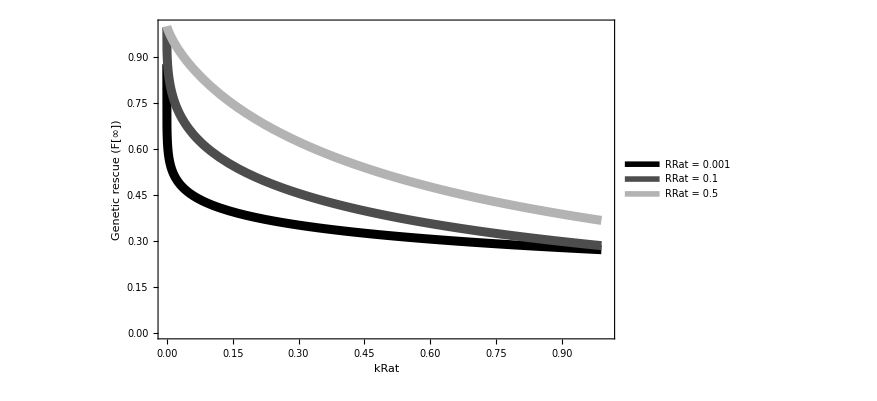

```mathematica
Legended[
Show[
Plot[1-Hypergeometric2F1[1,-Log[2]/eRRat,1-Log[2]/eRRat,-ⅇ^(-eRRat/2)/kRat]/(√2 Log[2])/.eRRat->Log[0.001],{kRat,0,0.99},PlotRange->{{0,1},{0,1}},PlotStyle->{Thickness[0.01],Black}],
Plot[1-Hypergeometric2F1[1,-Log[2]/eRRat,1-Log[2]/eRRat,-ⅇ^(-eRRat/2)/kRat]/(√2 Log[2])/.eRRat->Log[0.1],{kRat,0,0.99},PlotRange->{{0,1},{0,1}},PlotStyle->{Thickness[0.01],GrayLevel[0.3]}],
Plot[1-Hypergeometric2F1[1,-Log[2]/eRRat,1-Log[2]/eRRat,-ⅇ^(-eRRat/2)/kRat]/(√2 Log[2])/.eRRat->Log[0.5],{kRat,0,0.99},PlotRange->{{0,1},{0,1}},PlotStyle->{Thickness[0.01],GrayLevel[0.7]}],
Frame->True,
FrameLabel->{Style["kRat",LabelSize],Style["Genetic rescue (F[∞])",LabelSize]},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangeClipping->False
],
Placed[
LineLegend[{
Directive[Thickness[0.1],Black],
Directive[Thickness[0.1],GrayLevel[0.3]],
Directive[Thickness[0.1],GrayLevel[0.7]]
},
{
Style["RRat = 0.001",LabelSize],
Style["RRat = 0.1",LabelSize],
Style["RRat = 0.5", LabelSize]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.8,0.8}
] 
]
```

```mathematica
Export[imagedir<>"GeneticRescue2.eps",%];
```

```mathematica
Show[
Plot3D[Hypergeometric2F1[1,-Log[2]/eRRat,1-Log[2]/eRRat,-ⅇ^(-eRRat/2)/kRat]/(√2 Log[2])/.eRRat->Log[RRat],{kRat,0,0.99},{RRat,0,.99},PlotRange->{{0,1},{0,1}}],
AxesLabel->{Style["(SubscriptBox[N, I][0])/(SubscriptBox[N, R][0])",LabelSize],Style["W_R/W_I",LabelSize],Style["1-F_I[∞]",LabelSize]},
AxesStyle->Directive[FontSize->TickSize],
ImageSize->FigureSize,
PlotRangeClipping->False]
```

-Graphics3D-

```mathematica
Export[imagedir<>"GeneticRescue3D.eps",%];
```

```mathematica
1-Hypergeometric2F1[1,-Log[2]/eRRat,1-Log[2]/eRRat,-ⅇ^(-eRRat/2)/kRat]/(√2 Log[2])/.eRRat->Log[RRat]
```

1-Hypergeometric2F1[1,-Log[2]/Log[RRat],1-Log[2]/Log[RRat],-1/(kRat √RRat)]/(√2 Log[2])

We can take the Taylor series of this solution for kRat small,but it behaves poorly:

```mathematica
FullSimplify[Normal[Series[1-Hypergeometric2F1[1,-Log[2]/eRRat,1-Log[2]/eRRat,-ⅇ^(-eRRat/2)/kRat]/(√2 Log[2]),{kRat,0,1}]],{eRRat>0,kRat>0}]
```

1-(kRat^(-Log[2]/eRRat) π Csc[(π Log[2])/eRRat])/(2 eRRat)-(ⅇ^(eRRat/2) kRat)/(√2 (eRRat+Log[2]))

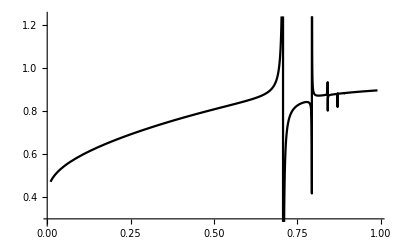

```mathematica
Plot[%/.eRRat->Log[RRat]/.kRat->0.1/.t->100,{RRat,0.01,0.99},PlotStyle->Black]
```

Freek: At this point, you might want to try the approximate solutions you had found before for the Hypergeometric, as they seemed to have the right form.

```mathematica
1-Hypergeometric2F1[1,-Log[2]/eRRat,1-Log[2]/eRRat,-ⅇ^(-eRRat/2)/kRat]/(√2 Log[2])/.eRRat->Log[RRat]/.RRat->RRes/RInv/.RInv->Exp[rInv]/.RRes->Exp[rRes]/.kRat->kInv/kRes//Simplify
```

1-Hypergeometric2F1[1,-Log[2]/Log[ⅇ^(-rInv+rRes)],1-Log[2]/Log[ⅇ^(-rInv+rRes)],-kRes/(√(ⅇ^(-rInv+rRes)) kInv)]/(√2 Log[2])

This hypergeometric can be written as a Beta function, see:

```mathematica
1+((-ⅇ^(-eRRat/2)/kRat)^(Log[2]/eRRat) Beta[-ⅇ^(-eRRat/2)/kRat,-Log[2]/eRRat,0])/(√2 eRRat)/.eRRat->Log[RRat]
```

1+((-1/(kRat √RRat))^(Log[2]/Log[RRat]) Beta[-1/(kRat √RRat),-Log[2]/Log[RRat],0])/(√2 Log[RRat])

Using complexexpand this can be rewriten as:

```mathematica
1+((1/(kRat^2 RRat))^(Log[2]/(2 Log[RRat])) ∫_0^(-1/(kRat √RRat)) ((t^2)^(-Log[2 RRat]/(2 Log[RRat])))/(-1+t))/(√2 Log[RRat])
```

### Approximation de novo

```mathematica
ShowPlotNew[kRat_] :=Show[
Plot[1-2^(-(100+1))-∑_(j=0)^(100-1) (2^(-1-j) kRat)/(ⅇ^(eRRat j)+kRat)/.eRRat->Log[RRat],{RRat,0.001,0.99},PlotStyle->Dashed,PlotRange->{{0,1},{0,1}}],
Plot[1-2^(-Log[kRat]/Log[ RRat])/Log[4]/.eRRat->Log[RRat],{RRat,0,1},PlotStyle->{Red},PlotRange->{{0,1},{0,1}}]]
```

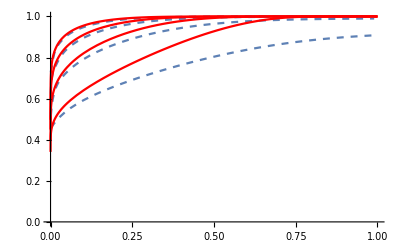

```mathematica
Show[
ShowPlotNew[0.0001],
ShowPlotNew[0.001],
ShowPlotNew[0.01],
ShowPlotNew[0.1]]
```

### Diffusion approximation

#### Numerically solve transitionmatrix

p_ij = the Probaility of going from i individuals to j individuals based on a poisson distribution

```mathematica
p[i_,j_,n_]:=If[j==n,1-CDF[PoissonDistribution[i(1+s)],n-1],Simplify[PDF[PoissonDistribution[i(1+s)],j],{j>=0 ,i>=0}]]
```

```mathematica
n=500;
```

```mathematica
s=0.08;
```

```mathematica
Tmtrx=Table[p[i,j,n],{j,0,n},{i,1,n-1}];
cArray=ConstantArray[0,n+1];
Tmtrx = Insert[Tmtrx // Transpose,cArray,1]//Transpose;
Tmtrx[[1,1]]=1;
Tmtrx= Insert[Tmtrx // Transpose,cArray,n+1]//Transpose;
Tmtrx[[n+1,n+1]]=1;
```

```mathematica
v=ConstantArray[0,n+1];
v[[2]]=1;
```

```mathematica
M=Chop[Tmtrx];
```

```mathematica
MatrixPower[M,25].v;
```

```mathematica
Clear[SimulateN]
SimulateN[t_]:=simulateN[t]=
Block[{Res=MatrixPower[M,t].v},
newFracer=N[(1/(1-Res[[1]]))*Sum[Res[[i]]*(i-1),{i,2,n+1}]];
{newFracer}
]
```

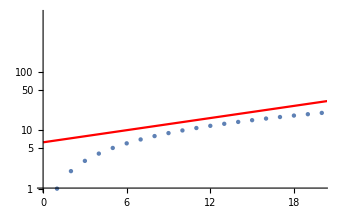

```mathematica
Show[
ListLogPlot[Table[{t,SimulateN[t][[1]]},{t,1,100}],PlotRange->{{0,20},{0,1000}}],
LogPlot[(1/0.16)*ⅇ^(t*0.08),{t,0,100},PlotStyle->Red]]
```

### Fixation probability

#### Introducing 1 allele

```mathematica
{1-P==Sum[PDF[PoissonDistribution[λ],j](1-P)^j,{j,0,Infinity}]}
```

{1-P==ⅇ^(-P λ)}

Haldane (1927) argued that the resident population was stable (λ ~ 1), and he focused on a beneficial allele, whose λ = 1+s when it first appeared (i.e., if as a heterozygote then s is the selection coefficient for the heterozygotes).  This assumes the allele’s fate is determined when rare and that the fate of all j offspring copies of the allele are independent.

We can define the expected number of kids per parent as 1+s (for an allele experiencing selection, s) or as 1+r (for a type growing at rate, r):

```mathematica
%/.λ->1+s
```

{1-P==ⅇ^(-P (1+s))}

s would be the selective coefficient for the rare allele in a haploid model and would be s = h s in a diploid model as long as the fate of the allele is decided while homozygotes remain rare (i.e., h isn’t too small and N isn’t too small)

```mathematica
Normal[Series[1-P-ⅇ^(-P (1+s))/.P->P ϵ/.s->s ϵ,{ϵ,0,2}]]
```

(-P^2/2+P s) ϵ^2

```mathematica
Solve[%==0,P]
```

{{P→0},{P→2 s}}

```mathematica
Solve[1-P==ⅇ^(-P (1+s)),P]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{P→(1+s+ProductLog[-ⅇ^(-1-s) (1+s)])/(1+s)}}

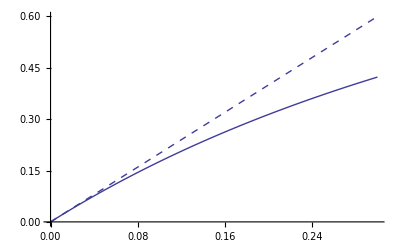

```mathematica
Show[Plot[2s,{s,0,0.3},PlotStyle->Dashed],Plot[(1+s+ProductLog[-ⅇ^(-1-s) (1+s)])/(1+s),{s,0,0.3}]]
```

The probabilty of establishment:

```mathematica
soln=(1+s+ProductLog[-ⅇ^(-1-s) (1+s)])/(1+s);
```

Probability that all k alleles would be lost if you start with k alleles would be: (full recombination)

```mathematica
(1-soln)^k;
```

So the probability that at least one survives when you start with k would be:

```mathematica
solnk=1-(1-a)^k/.a->soln//FullSimplify
```

1-(-ProductLog[-ⅇ^(-1-s) (1+s)]/(1+s))^k

k introduced alleles

```mathematica
{1-P[k]==Sum[PDF[PoissonDistribution[λ k],j](1-P[1])^j,{j,0,Infinity}]}
```

{1-P[k]==ⅇ^(-k λ P[1])}

```mathematica
%/.λ->1+s
```

{1-P[k]==ⅇ^(-k (1+s) P[1])}

```mathematica
Factor[Normal[Series[1-P[k]-ⅇ^(-P[1] k (1+s))/.P[1]->2 s/.P[k]->P[k] ϵ/.s->s ϵ,{ϵ,0,1}]]]
```

ϵ (2 k s-P[k])

```mathematica
Solve[%==0,P[k]]//Simplify
```

{{P[k]→2 k s}}

```mathematica
Solve[1-P[k]==ⅇ^(-k (1+s) P[1])/.P[1]->(1+s+ProductLog[-ⅇ^(-1-s) (1+s)])/(1+s),P[k]]
```

{{P[k]→1-ⅇ^(-k (1+s+ProductLog[-ⅇ^(-1-s) (1+s)]))}}

```mathematica
Solve[1-P[k]==ⅇ^(-k (1+s+ProductLog[-ⅇ^(-1-s) (1+s)])),P[k]]//FullSimplify
```

{{P[k]→1-ⅇ^(-k (1+s+ProductLog[-ⅇ^(-1-s) (1+s)]))}}

Also Kimura (1957) used a diffusion approximation to show that the p of eventual fixation of an allele starting at f p with additive selective effects s is:

```mathematica
(1-Exp[-4N s p])/(1-Exp[-4 N s])/.s->Log[1.01]/.p->10/N/.N->100
```

0.334598

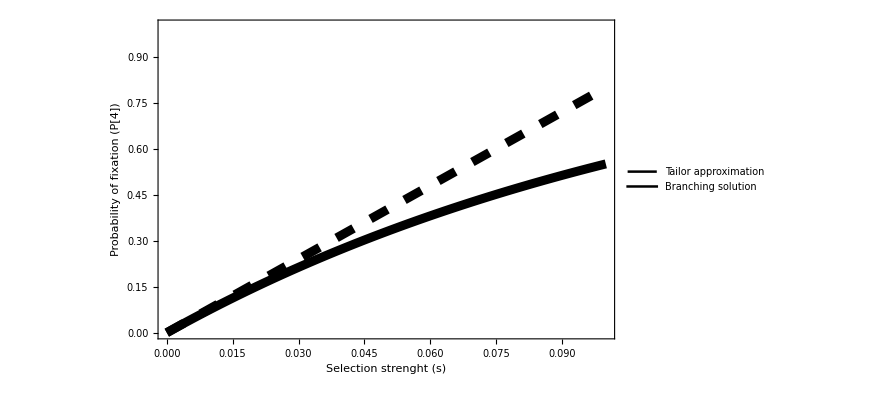

```mathematica
Legended[
Show[
Plot[2s k/.k->4,{s,0,0.1},PlotRange->{{0,0.1},{0,1}},PlotStyle->{Thickness[0.01],Black,Dashing[Large]}],
Plot[1-ⅇ^(-2 k s)/.k->4,{s,0,0.1},PlotStyle->{Thickness[0.01],Black}],
Frame->True,
FrameLabel->{Style["Selection strenght (s)",LabelSize],Style["Probability of fixation (P[4])",LabelSize]},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangeClipping->False
],
Placed[
LineLegend[{
Directive[Thickness[0.01],Black,Dashing[Large]],
Directive[Thickness[0.01],Black]
},
{
Style["Tailor approximation",LabelSize],
Style["Branching solution",LabelSize]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.3,0.8}
] 
]
```

```mathematica
Export[imagedir<>"FixationProbability.eps",%];
```

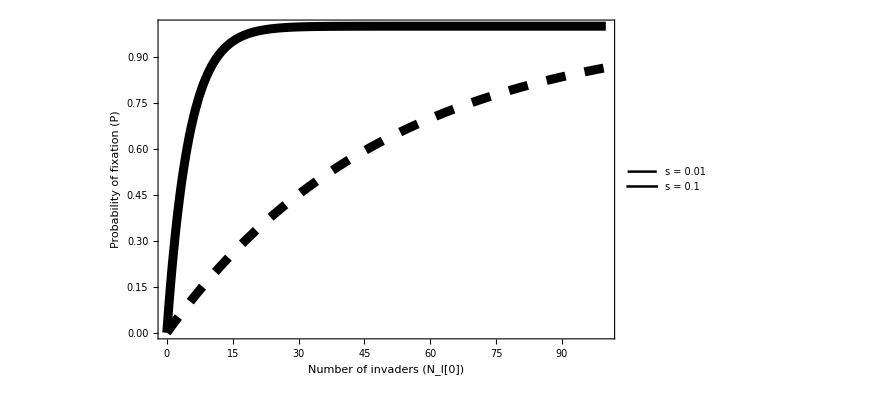

```mathematica
Legended[
Show[
Plot[1-ⅇ^(-2 k s)/.s->1/100,{k,0,100},PlotRange->{Automatic,{0,1}},PlotStyle->{Thickness[0.01],Black,Dashing[Large]}],
Plot[1-ⅇ^(-2 k s)/.s->1/10,{k,0,100},PlotRange->{Automatic,{0,1}},PlotStyle->{Thickness[0.01],Black,Solid}],
Frame->True,
FrameLabel->{Style["Number of invaders (N_I[0])",LabelSize],Style["Probability of fixation (P)",LabelSize]},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangeClipping->False
],
Placed[
LineLegend[{
Directive[Thickness[0.01],Black,Dashing[Large]],
Directive[Thickness[0.01],Black]
},
{
Style["s = 0.01",LabelSize],
Style["s = 0.1",LabelSize]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.8,0.2}
] 
]
```

```mathematica
Export[imagedir<>"FixationProbability2.eps",%];
```

```mathematica
1-ⅇ^(-2 k s)/.k->10/.s->0.05
```

0.632121

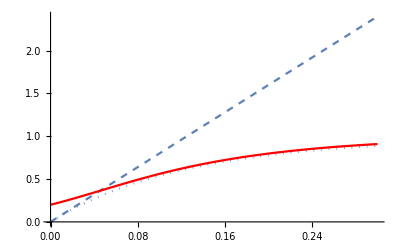

1-2^(-(100+1))-∑_(j=0)^(100-1) (2^(-1-j) kRat)/(ⅇ^(eRRat j)+kRat)

### Analysis probability * rescue

```mathematica
1-ⅇ^(-2 k s)/.k->kInv/.s->rInv
```

1-ⅇ^(-2 kInv rInv)

```mathematica
1-Hypergeometric2F1[1,-Log[2]/Log[ⅇ^(-rInv+rRes)],1-Log[2]/Log[ⅇ^(-rInv+rRes)],-kRes/(√(ⅇ^(-rInv+rRes)) kInv)]/(√2 Log[2])
```

1-Hypergeometric2F1[1,-Log[2]/Log[ⅇ^(-rInv+rRes)],1-Log[2]/Log[ⅇ^(-rInv+rRes)],-kRes/(√(ⅇ^(-rInv+rRes)) kInv)]/(√2 Log[2])

```mathematica
ShowPlot[s_,kRes_,rRes_]:=Show[
Plot[1-ⅇ^(-2 k s),{k,0,100},PlotStyle->Red,PlotRange->{{0,100},{0,1}}],
Plot[1-Hypergeometric2F1[1,-Log[2]/Log[ⅇ^(rRes-s)],1-Log[2]/Log[ⅇ^(rRes-s)],-kRes/(√(ⅇ^(rRes-s)) k)]/(√2 Log[2]),{k,0,100},PlotStyle->{Black}],
Plot[(1-Hypergeometric2F1[1,-Log[2]/Log[ⅇ^(rRes-s)],1-Log[2]/Log[ⅇ^(rRes-s)],-kRes/(√(ⅇ^(rRes-s)) k)]/(√2 Log[2]))*(1-ⅇ^(-2 k s)),{k,0,100},PlotStyle->{Blue,Dotted}]
]
```

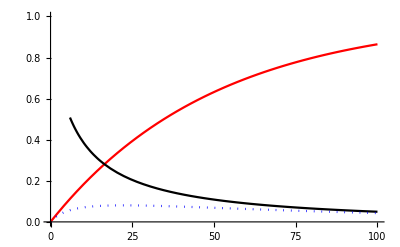

```mathematica
ShowPlot[0.01,10,-0.5]
```

```mathematica
D[(1-Hypergeometric2F1[1,-Log[2]/Log[ⅇ^(-rInv+rRes)],1-Log[2]/Log[ⅇ^(-rInv+rRes)],-kRes/(√(ⅇ^(-rInv+rRes)) kInv)]/(√2 Log[2]))*(1-ⅇ^(-2 kInv rInv)),kInv]//FullSimplify
```

```mathematica
Solve[1/2 ⅇ^(-2 kInv rInv) (4 rInv-(√2 √(ⅇ^(-rInv+rRes)) (-1+ⅇ^(2 kInv rInv)))/((√(ⅇ^(-rInv+rRes)) kInv+kRes) Log[ⅇ^(-rInv+rRes)])+(√2 ((-1+ⅇ^(2 kInv rInv)) Log[2]-2 kInv rInv Log[ⅇ^(-rInv+rRes)]))/(kInv Log[2] Log[ⅇ^(-rInv+rRes)]))==0,kInv]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[1/2 ⅇ^(-2 kInv rInv) (4 rInv-(√2 √(ⅇ^(-rInv+rRes)) (-1+ⅇ^(2 kInv rInv)))/((√(ⅇ^(-rInv+rRes)) kInv+kRes) Log[ⅇ^(-rInv+rRes)])+(√2 ((-1+ⅇ^(2 kInv rInv)) Log[2]-2 kInv rInv Log[ⅇ^(-rInv+rRes)]))/(kInv Log[2] Log[ⅇ^(-rInv+rRes)]))==0,kInv]

## Analysis genetic rescue

Genomic swamping

```mathematica
1-Hypergeometric2F1[1,-Log[2]/Log[RRes/RInv],1-Log[2]/Log[RRes/RInv],-kRes/(kInv √(RRes/RInv))]/(√2 Log[2])
```

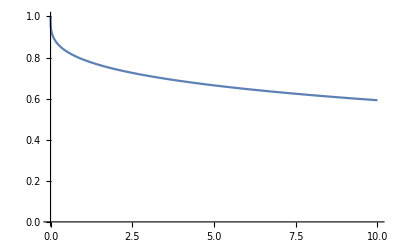

```mathematica
Plot[1-Hypergeometric2F1[1,-Log[2]/Log[RRes/RInv],1-Log[2]/Log[RRes/RInv],-kRes/(kInv √(RRes/RInv))]/(√2 Log[2])/.kRes->100/.RRes->0.1/.RInv->1.01,{kInv,0,10},PlotRange->{Automatic,{0,1}}]
```

Demographic swamping

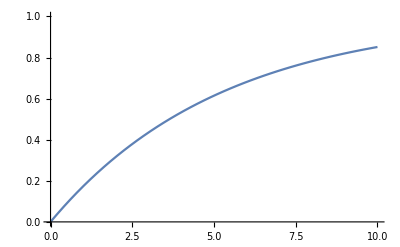

```mathematica
Plot[1-RInv^(-2 kInv)/.RInv->1.1,{kInv,0,10},PlotRange->{Automatic,{0,1}}]
```

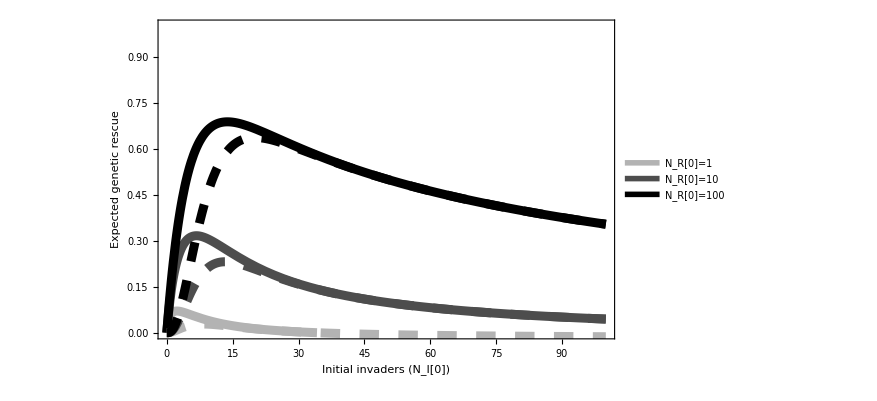

```mathematica
Legended[
Show[
Plot[(1-RInv^(-2 kInv))^k (1-1/Log[4] √2 Hypergeometric2F1[1,-Log[2]/Log[RRes/RInv],1-Log[2]/Log[RRes/RInv],-kRes/(kInv √(RRes/RInv))])/.k->1/.kRes->1/.RRes->0.5/.RInv->1.1,{kInv,0,100},PlotRange->{Automatic,{0,1}},PlotStyle->{Thickness[0.01],GrayLevel[0.7]}],
Plot[(1-RInv^(-2 kInv))^k (1-1/Log[4] √2 Hypergeometric2F1[1,-Log[2]/Log[RRes/RInv],1-Log[2]/Log[RRes/RInv],-kRes/(kInv √(RRes/RInv))])/.k->1/.kRes->10/.RRes->0.5/.RInv->1.1,{kInv,0,100},PlotStyle->{Thickness[0.01],GrayLevel[0.3]}],
Plot[(1-RInv^(-2 kInv))^k (1-1/Log[4] √2 Hypergeometric2F1[1,-Log[2]/Log[RRes/RInv],1-Log[2]/Log[RRes/RInv],-kRes/(kInv √(RRes/RInv))])/.k->1/.kRes->100/.RRes->0.5/.RInv->1.1,{kInv,0,100},PlotStyle->{Thickness[0.01],Black}],
Plot[(1-RInv^(-2 kInv))^k (1-1/Log[4] √2 Hypergeometric2F1[1,-Log[2]/Log[RRes/RInv],1-Log[2]/Log[RRes/RInv],-kRes/(kInv √(RRes/RInv))])/.k->3/.kRes->1/.RRes->0.5/.RInv->1.1,{kInv,0,100},PlotStyle->{Thickness[0.01],GrayLevel[0.7],Dashing[Large]}],
Plot[(1-RInv^(-2 kInv))^k (1-1/Log[4] √2 Hypergeometric2F1[1,-Log[2]/Log[RRes/RInv],1-Log[2]/Log[RRes/RInv],-kRes/(kInv √(RRes/RInv))])/.k->3/.kRes->10/.RRes->0.5/.RInv->1.1,{kInv,0,100},PlotStyle->{Thickness[0.01],GrayLevel[0.3],Dashing[Large]}],
Plot[(1-RInv^(-2 kInv))^k (1-1/Log[4] √2 Hypergeometric2F1[1,-Log[2]/Log[RRes/RInv],1-Log[2]/Log[RRes/RInv],-kRes/(kInv √(RRes/RInv))])/.k->3/.kRes->100/.RRes->0.5/.RInv->1.1,{kInv,0,100},PlotStyle->{Thickness[0.01],Black,Dashing[Large]}],
Frame->True,
FrameLabel->{Style["Initial invaders (N_I[0])",LabelSize],Style["Expected genetic rescue",LabelSize]},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangeClipping->False
],
Placed[
LineLegend[{
Directive[Thickness[0.1],GrayLevel[0.7]],
Directive[Thickness[0.1],GrayLevel[0.3]],
Directive[Thickness[0.1],Black]
},
{
Style["N_R[0]=1",LabelSize],
Style["N_R[0]=10",LabelSize],
Style["N_R[0]=100",LabelSize]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.8,0.8}
] 
]
```

```mathematica
Export[imagedir<>"GeneticRescue.eps",%];
```

```mathematica
D[(1-RInv^(-2 kInv))^k (1-(√2 Hypergeometric2F1[1,-Log[2]/Log[RRes/RInv],1-Log[2]/Log[RRes/RInv],-kRes/(kInv √(RRes/RInv))])/Log[4]),kInv]
```

/.k→1/.kRes→100/.RRes→0.5/.RInv→1.1

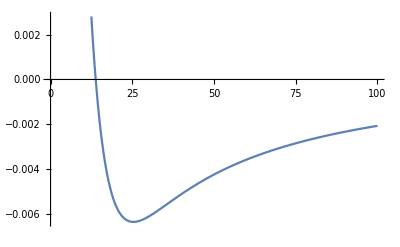

```mathematica
Plot[2 k RInv^(-2 kInv) (1-RInv^(-2 kInv))^(-1+k) (1-1/Log[4] √2 Hypergeometric2F1[1,-Log[2]/Log[RRes/RInv],1-Log[2]/Log[RRes/RInv],-kRes/(kInv √(RRes/RInv))]) Log[RInv]-(√2 (1-RInv^(-2 kInv))^k (1/(1+kRes/(kInv √(RRes/RInv)))-Hypergeometric2F1[1,-Log[2]/Log[RRes/RInv],1-Log[2]/Log[RRes/RInv],-kRes/(kInv √(RRes/RInv))]) Log[2])/(kInv Log[4] Log[RRes/RInv])/.k->1/.kRes->100/.RRes->0.5/.RInv->1.1,{kInv,0,100}]
```

```mathematica
Solve[2 k RInv^(-2 kInv) (1-RInv^(-2 kInv))^(-1+k) (1-1/Log[4] √2 Hypergeometric2F1[1,-Log[2]/Log[RRes/RInv],1-Log[2]/Log[RRes/RInv],-kRes/(kInv √(RRes/RInv))]) Log[RInv]-(√2 (1-RInv^(-2 kInv))^k (1/(1+kRes/(kInv √(RRes/RInv)))-Hypergeometric2F1[1,-Log[2]/Log[RRes/RInv],1-Log[2]/Log[RRes/RInv],-kRes/(kInv √(RRes/RInv))]) Log[2])/(kInv Log[4] Log[RRes/RInv])==0/.k->1/.kRes->100/.RRes->1/2/.RInv->2,kInv]
```

{{}}

```mathematica
-Log[1-P]/(2 Log[RInv])/.P->0.999/.RInv->1.01
```

347.112

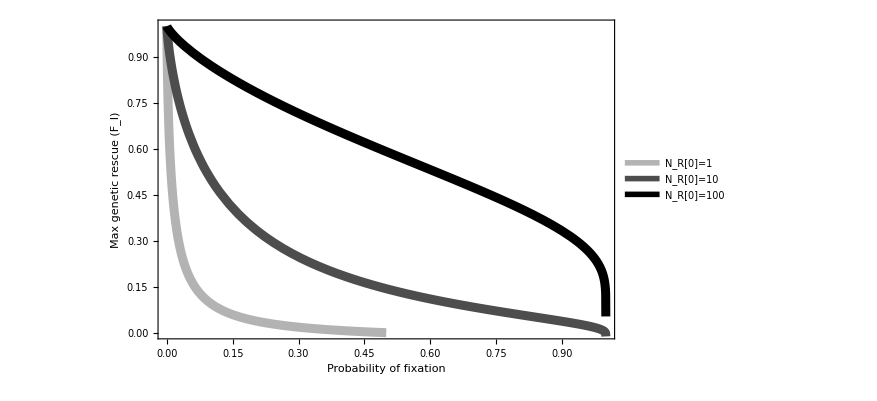

```mathematica
Legended[
Show[
Plot[1-1/(√2 Log[2])Hypergeometric2F1[1,-Log[2]/Log[RRes/RInv],1-Log[2]/Log[RRes/RInv],-kRes/(kInv √(RRes/RInv))]/.kInv->-Log[1-P]/(2 Log[RInv])/.kRes->1/.RRes->0.5/.RInv->1.01,{P,0,1},PlotRange->{Automatic,{0,1}},PlotStyle->{Thickness[0.01],GrayLevel[0.7]}],
Plot[1-1/(√2 Log[2])Hypergeometric2F1[1,-Log[2]/Log[RRes/RInv],1-Log[2]/Log[RRes/RInv],-kRes/(kInv √(RRes/RInv))]/.kInv->-Log[1-P]/(2 Log[RInv])/.kRes->10/.RRes->0.5/.RInv->1.01,{P,0,1},PlotStyle->{Thickness[0.01],GrayLevel[0.3]}],
Plot[1-1/(√2 Log[2])Hypergeometric2F1[1,-Log[2]/Log[RRes/RInv],1-Log[2]/Log[RRes/RInv],-kRes/(kInv √(RRes/RInv))]/.kInv->-Log[1-P]/(2 Log[RInv])/.kRes->100/.RRes->0.5/.RInv->1.01,{P,0,1},PlotStyle->{Thickness[0.01],Black}],
Frame->True,
FrameLabel->{Style["Probability of fixation",LabelSize],Style["Max genetic rescue (F_I)",LabelSize]},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangeClipping->False
],
Placed[
LineLegend[{
Directive[Thickness[0.1],GrayLevel[0.7]],
Directive[Thickness[0.1],GrayLevel[0.3]],
Directive[Thickness[0.1],Black]
},
{
Style["N_R[0]=1",LabelSize],
Style["N_R[0]=10",LabelSize],
Style["N_R[0]=100",LabelSize]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.8,0.8}
] 
]
```

```mathematica
Export[imagedir<>"GeneticRescue2.eps",%];
```

```mathematica
1-1/(√2 Log[2])Hypergeometric2F1[1,-Log[2]/Log[RRes/RInv],1-Log[2]/Log[RRes/RInv],-kRes/(kInv √(RRes/RInv))]/.kInv->-Log[1-P]/(2 Log[RInv])//FullSimplify
```

1-(√2 Hypergeometric2F1[1,-Log[2]/Log[RRes/RInv],1-Log[2]/Log[RRes/RInv],(2 kRes Log[RInv])/(√(RRes/RInv) Log[1-P])])/Log[4]

```mathematica
D[(1-RInv^(-2 kInv))^k (1-1/Log[4] √2 Hypergeometric2F1[1,-Log[2]/Log[RRes/RInv],1-Log[2]/Log[RRes/RInv],-kRes/(kInv √(RRes/RInv))]),kRes]
```

(√2 (1-RInv^(-2 kInv))^k (1/(1+kRes/(kInv √(RRes/RInv)))-Hypergeometric2F1[1,-Log[2]/Log[RRes/RInv],1-Log[2]/Log[RRes/RInv],-kRes/(kInv √(RRes/RInv))]) Log[2])/(kRes Log[4] Log[RRes/RInv])

```mathematica
F'[kInv_]:=(√2 (1-RInv^(-2 kInv))^k (1/(1+kRes/(kInv √(RRes/RInv)))-Hypergeometric2F1[1,-Log[2]/Log[RRes/RInv],1-Log[2]/Log[RRes/RInv],-kRes/(kInv √(RRes/RInv))]) Log[2])/(kRes Log[4] Log[RRes/RInv])/.kRes->100/.RRes->0.5/.RInv->1.1/.k->1
```

```mathematica
F'[2]
```

0.000164438

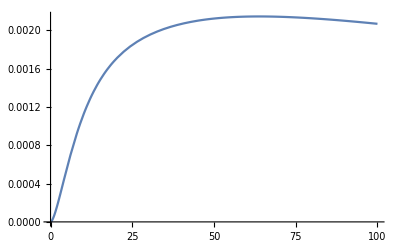

```mathematica
Plot[F'[kInv],{kInv,0,100},PlotRange->All]
```

## Simulation listplots manual input

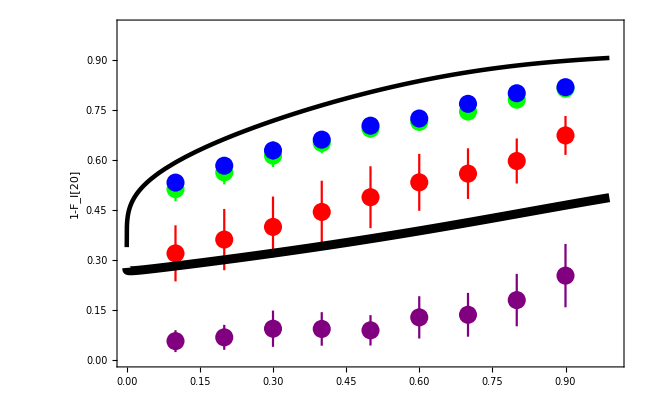

```mathematica
(*HAPLOIDS*)
Show[
ErrorListPlot[{
{{0.1,0.513046},ErrorBar[0.0359775]},
{{0.2,0.563185},ErrorBar[0.0359873]},
{{0.3,0.613274},ErrorBar[0.0337924]},
{{0.4,0.651559},ErrorBar[0.0310784]},
{{0.5,0.694475},ErrorBar[0.0265394]},
{{0.6,0.714826},ErrorBar[0.0263339]},
{{0.7,0.745588},ErrorBar[0.0222459]},
{{0.8,0.781247},ErrorBar[0.0172995]},
{{0.9,0.814127},ErrorBar[0.0142396]}},
PlotRange->{{0,1},{0,1}},
PlotStyle->{Green,PointSize[0.02]}],
ErrorListPlot[{
{{0.1,0.532602},ErrorBar[0.0251662]},
{{0.2,0.583251},ErrorBar[0.0236113]},
{{0.3,0.629031},ErrorBar[0.0265806]},
{{0.4,0.661419},ErrorBar[0.0224998]},
{{0.5,0.703267},ErrorBar[0.0205241]},
{{0.6,0.724778},ErrorBar[0.0199775]},
{{0.7,0.768755},ErrorBar[0.0157577]},
{{0.8,0.800482},ErrorBar[0.0117161]},
{{0.9,0.818699},ErrorBar[0.0109792]}},
PlotRange->{{0,1},{0,1}},PlotStyle->{Blue,PointSize[0.02]}],
ErrorListPlot[{
{{0.1,0.320403},ErrorBar[0.0841093]},
{{0.2,0.361823},ErrorBar[0.091837]},
{{0.3,0.399748},ErrorBar[0.0910838]},
{{0.4,0.444715},ErrorBar[0.0935371]},
{{0.5,0.488809},ErrorBar[0.0928564]},
{{0.6,0.533417},ErrorBar[0.0853627]},
{{0.7,0.559548},ErrorBar[0.0759159]},
{{0.8,0.597386},ErrorBar[0.0675406]},
{{0.9,0.674047},ErrorBar[0.0583348]}},
PlotRange->{{0,1},{0,1}},PlotStyle->{Red,PointSize[0.02]}],
ErrorListPlot[{
{{0.1,0.0573324},ErrorBar[0.0328555]},
{{0.2,0.0686867},ErrorBar[0.037404]},
{{0.3,0.094562},ErrorBar[0.054382]},
{{0.4,0.0938591},ErrorBar[0.050292]},
{{0.5,0.0897132},ErrorBar[0.0455834]},
{{0.6,0.128539},ErrorBar[0.0634337]},
{{0.7,0.136306},ErrorBar[0.0656726]},
{{0.8,0.180347},ErrorBar[0.0785448]},
{{0.9,0.253699},ErrorBar[0.0950139]}},
PlotRange->{{0,1},{0,1}},PlotStyle->{Purple,PointSize[0.02]}],
Plot[1-Hypergeometric2F1[1,-Log[2]/Log[RRat],1-Log[2]/Log[RRat],-1/(kRat √RRat)]/(√2 Log[2])/.kRat->1/10,{RRat,0,0.99},PlotStyle->{Black,Thickness[0.005]}],
Plot[1-Hypergeometric2F1[1,-Log[2]/Log[RRat],1-Log[2]/Log[RRat],-1/(kRat √RRat)]/(√2 Log[2])/.kRat->10/10,{RRat,0,0.99},PlotStyle->{Black,Thickness[0.01]}],
Frame->True,

FrameLabel->{Style["",LabelSize],Style["1-F_I[20]",LabelSize]},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangeClipping->False
]
```

```mathematica
Export[imagedir<>"Simulation1.eps",%];
```

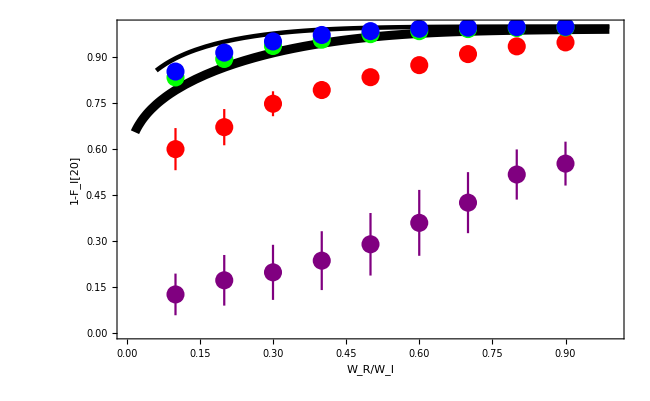

```mathematica
(*HAPLOIDS*)
Show[
ErrorListPlot[{
{{0.1,0.598844},ErrorBar[0.068707]},
{{0.2,0.670572},ErrorBar[0.0590695]},
{{0.3,0.746954},ErrorBar[0.0406857]},
{{0.4,0.79172},ErrorBar[0.0293246]},
{{0.5,0.833575},ErrorBar[0.0221356]},
{{0.6,0.872904},ErrorBar[0.01222]},
{{0.7,0.908928},ErrorBar[0.00652701]},
{{0.8,0.934157},ErrorBar[0.00292066]},
{{0.9,0.947041},ErrorBar[0.00194316]}},
PlotRange->{{0,1},{0,1}},PlotStyle->{Red,PointSize[0.02]}],
ErrorListPlot[{
{{0.1,0.124904},ErrorBar[0.0679469]},
{{0.2,0.171003},ErrorBar[0.0825718]},
{{0.3,0.19698},ErrorBar[0.0898352]},
{{0.4,0.235088},ErrorBar[0.0959802]},
{{0.5,0.288497},ErrorBar[0.101999]},
{{0.6,0.358405},ErrorBar[0.107495]},
{{0.7,0.424284},ErrorBar[0.0995503]},
{{0.8,0.516108},ErrorBar[0.0818168]},
{{0.9,0.55168},ErrorBar[0.071582]}},
PlotRange->{{0,1},{0,1}},PlotStyle->{Purple,PointSize[0.02]}],
Plot[1-Hypergeometric2F1[1,-Log[2]/Log[RRat],1-Log[2]/Log[RRat],-1/(kRat √RRat)]/(√2 Log[2])/.kRat->1/1000,{RRat,0,0.99},PlotStyle->{Black,Thickness[0.005]}],
Plot[1-Hypergeometric2F1[1,-Log[2]/Log[RRat],1-Log[2]/Log[RRat],-1/(kRat √RRat)]/(√2 Log[2])/.kRat->10/1000,{RRat,0,0.99},PlotStyle->{Black,Thickness[0.01]}],
ErrorListPlot[{
{{0.1,0.832742},ErrorBar[0.00872175]},
{{0.2,0.893034},ErrorBar[0.00441898]},
{{0.3,0.935316},ErrorBar[0.0025233]},
{{0.4,0.955873},ErrorBar[0.00131179]},
{{0.5,0.973962},ErrorBar[0.000627735]},
{{0.6,0.983722},ErrorBar[0.000298806]},
{{0.7,0.990539},ErrorBar[0.000122489]},
{{0.8,0.99397},ErrorBar[4.35 10^-5]},
{{0.9,0.995807},ErrorBar[2.24 10^-5]}},
PlotRange->{{0,1},{0,1}},PlotStyle->{Green,PointSize[0.02]}],
ErrorListPlot[{
{{0.1,0.852004},ErrorBar[0.00372432]},
{{0.2,0.913735},ErrorBar[0.00182244]},
{{0.3,0.950223},ErrorBar[0.000918692]},
{{0.4,0.971311},ErrorBar[0.000458062]},
{{0.5,0.983837},ErrorBar[0.000232059]},
{{0.6,0.991473},ErrorBar[8.72 10^-5]},
{{0.7,0.995211},ErrorBar[3.95 10^-5]},
{{0.8,0.996937},ErrorBar[1.54 10^-5]},
{{0.9,0.997735},ErrorBar[7.68 10^-6]}},
PlotRange->{{0,1},{0,1}},PlotStyle->{Blue,,PointSize[0.02]}],
Frame->True,
FrameLabel->{Style["W_R/W_I",LabelSize],Style["1-F_I[20]",LabelSize]},
FrameStyle->Directive[FontSize->TickSize],
ImageSize->FigureSize,
PlotRangeClipping->False
]
```

```mathematica
Export[imagedir<>"Simulation2.eps",%];
```

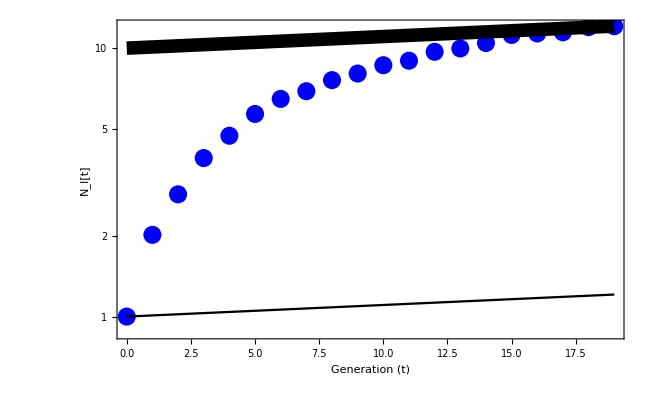

```mathematica
Show[
ListLogPlot[{{0,1.0000000},{1,2.015707},{2,2.853403},{3,3.895288},{4,4.717277},{5,5.685864},{6,6.471204},{7,6.910995},{8,7.602094},{9,8.041885},{10,8.638743},{11,8.979058},{12,9.691099},{13,9.973822},{14,10.450262},{15,11.198953},{16,11.340314},{17,11.455497},
{18,11.973822},{19,12.073298},},PlotStyle->{PointSize[0.02],Blue}],
LogPlot[1.01^t,{t,0,19},PlotStyle->{Black,Thickness[0.0025]}],
LogPlot[10 1.01^t,{t,0,19},PlotStyle->{Black,Thickness[0.015]}],
Frame->True,
FrameLabel->{Style["Generation (t)",LabelSize],Style["N_I[t]",LabelSize]},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangeClipping->False
]
```

```mathematica
Export[imagedir<>"SimvsNum.eps",%];
```

```mathematica
ListPlot[{testData1,testData2,testData3},PlotMarkers->{{●,10},{▲,10},{■,10}}]
```

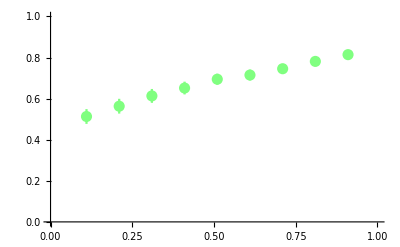

```mathematica
ErrorListPlot[{
{{0.11,0.513046},ErrorBar[0.0359775]},
{{0.21,0.563185},ErrorBar[0.0359873]},
{{0.31,0.613274},ErrorBar[0.0337924]},
{{0.41,0.651559},ErrorBar[0.0310784]},
{{0.51,0.694475},ErrorBar[0.0265394]},
{{0.61,0.714826},ErrorBar[0.0263339]},
{{0.71,0.745588},ErrorBar[0.0222459]},
{{0.81,0.781247},ErrorBar[0.0172995]},
{{0.91,0.814127},ErrorBar[0.0142396]}},
PlotRange->{{0,1},{0,1}},
PlotStyle->{Lighter[Green,0.5],PointSize[0.02]}]
```

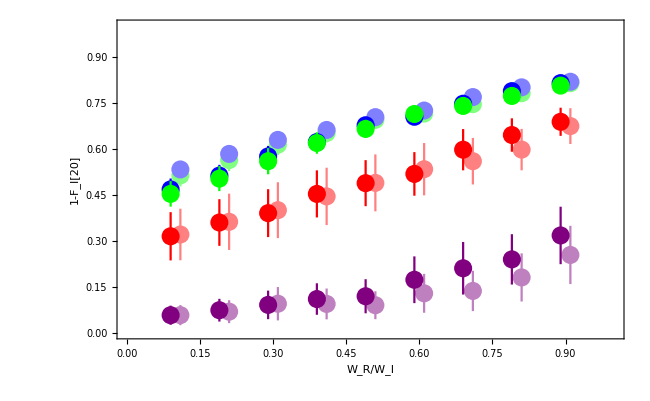

```mathematica
(*HAPLOIDSvsDIPLOIDS
ListPlot[{testData1,testData2,testData3},PlotMarkers->{{●,10},{▲,10},{■,10}}]*)
Show[
ErrorListPlot[{
{{0.11,0.513046},ErrorBar[0.0359775]},
{{0.21,0.563185},ErrorBar[0.0359873]},
{{0.31,0.613274},ErrorBar[0.0337924]},
{{0.41,0.651559},ErrorBar[0.0310784]},
{{0.51,0.694475},ErrorBar[0.0265394]},
{{0.61,0.714826},ErrorBar[0.0263339]},
{{0.71,0.745588},ErrorBar[0.0222459]},
{{0.81,0.781247},ErrorBar[0.0172995]},
{{0.91,0.814127},ErrorBar[0.0142396]}},
PlotRange->{{0,1},{0,1}},
PlotStyle->{Lighter[Green,0.5],PointSize[0.02]},
Ticks->{0,1,0.1}],
ErrorListPlot[{
{{0.11,0.532602},ErrorBar[0.0251662]},
{{0.21,0.583251},ErrorBar[0.0236113]},
{{0.31,0.629031},ErrorBar[0.0265806]},
{{0.41,0.661419},ErrorBar[0.0224998]},
{{0.51,0.703267},ErrorBar[0.0205241]},
{{0.61,0.724778},ErrorBar[0.0199775]},
{{0.71,0.768755},ErrorBar[0.0157577]},
{{0.81,0.800482},ErrorBar[0.0117161]},
{{0.91,0.818699},ErrorBar[0.0109792]}},
PlotRange->{{0,1},{0,1}},PlotStyle->{Lighter[Blue,.5],PointSize[0.02]}],
ErrorListPlot[{
{{0.11,0.320403},ErrorBar[0.0841093]},
{{0.21,0.361823},ErrorBar[0.091837]},
{{0.31,0.399748},ErrorBar[0.0910838]},
{{0.41,0.444715},ErrorBar[0.0935371]},
{{0.51,0.488809},ErrorBar[0.0928564]},
{{0.61,0.533417},ErrorBar[0.0853627]},
{{0.71,0.559548},ErrorBar[0.0759159]},
{{0.81,0.597386},ErrorBar[0.0675406]},
{{0.91,0.674047},ErrorBar[0.0583348]}},
PlotRange->{{0,1},{0,1}},PlotStyle->{Lighter[Red,.5],PointSize[0.02]}],
ErrorListPlot[{
{{0.11,0.0573324},ErrorBar[0.0328555]},
{{0.21,0.0686867},ErrorBar[0.037404]},
{{0.31,0.094562},ErrorBar[0.054382]},
{{0.41,0.0938591},ErrorBar[0.050292]},
{{0.51,0.0897132},ErrorBar[0.0455834]},
{{0.61,0.128539},ErrorBar[0.0634337]},
{{0.71,0.136306},ErrorBar[0.0656726]},
{{0.81,0.180347},ErrorBar[0.0785448]},
{{0.91,0.253699},ErrorBar[0.0950139]}},
PlotRange->{{0,1},{0,1}},PlotStyle->{Lighter[Purple,.5],PointSize[0.02]}],
ErrorListPlot[{
{{0.09,0.467542},ErrorBar[0.0356149]},
{{0.19,0.512674},ErrorBar[0.0349405]},
{{0.29,0.575275},ErrorBar[0.034197]},
{{0.39,0.621984},ErrorBar[0.026727]},
{{0.49,0.676819},ErrorBar[0.0238624]},
{{0.59,0.704487},ErrorBar[0.0220144]},
{{0.69,0.747003},ErrorBar[0.0184656]},
{{0.79,0.788167},ErrorBar[0.0139775]},
{{0.89,0.814233},ErrorBar[0.0121484]}},
PlotRange->{{0,1},{0,1}},PlotStyle->{Blue,PointSize[0.02]}],
ErrorListPlot[{
{{0.09,0.452947},ErrorBar[0.0416762]},
{{0.19,0.502782},ErrorBar[0.0409243]},
{{0.29,0.559552},ErrorBar[0.04278]},
{{0.39,0.618929},ErrorBar[0.0350555]},
{{0.49,0.664916},ErrorBar[0.0294758]},
{{0.59,0.71345},ErrorBar[0.0231087]},
{{0.69,0.739841},ErrorBar[0.0203134]},
{{0.79,0.772394},ErrorBar[0.018793]},
{{0.89,0.806177},ErrorBar[0.0135045]}},
PlotRange->{{0,1},{0,1}}, PlotStyle->{Green,PointSize[0.02]}],
ErrorListPlot[{
{{0.09,0.314579},ErrorBar[0.0787097]},
{{0.19,0.359514},ErrorBar[0.0761455]},
{{0.29,0.390063},ErrorBar[0.0781205]},
{{0.39,0.452843},ErrorBar[0.0768475]},
{{0.49,0.487888},ErrorBar[0.0751037]},
{{0.59,0.518019},ErrorBar[0.0711282]},
{{0.69,0.597039},ErrorBar[0.0672876]},
{{0.79,0.644942},ErrorBar[0.0544734]},
{{0.89,0.688085},ErrorBar[0.0458834]}},
PlotRange->{{0,1},{0,1}},PlotStyle->{Red,PointSize[0.02]}],
ErrorListPlot[{
{{0.09,0.0571124},ErrorBar[0.0312194]},
{{0.19,0.0734142},ErrorBar[0.0370664]},
{{0.29,0.0907734},ErrorBar[0.0465685]},
{{0.39,0.109875},ErrorBar[0.0513698]},
{{0.49,0.118939},ErrorBar[0.0555848]},
{{0.59,0.172753},ErrorBar[0.0762544]},
{{0.69,0.210194},ErrorBar[0.0857007]},
{{0.79,0.23927},ErrorBar[0.0821213]},
{{0.89,0.317342},ErrorBar[0.0937329]}},
PlotRange->{{0,1},{0,1}},PlotStyle->{Purple,PointSize[0.02]}],
Frame->True,

FrameLabel->{Style["W_R/W_I",LabelSize],Style["1-F_I[20]",LabelSize]},
FrameStyle->Directive[FontSize->TickSize],
ImageSize->FigureSize,
PlotRangeClipping->False
]
```

```mathematica
Export[imagedir<>"SimulationHaploidvsDiploid.eps",%];
```